# Three-link Swimmer with Varying Stiffness and Amplitude

```mathematica
Needs["MaTeX`"]
```

The obvious thing to do is start by reproducing the three-link using Scott’s notebook as a guide.

```mathematica
robotParameters = {a -> 0.0725, b-> 0.15, gap-> 0.02};
```

```mathematica
zbody = {x[t], y[t]};
```

```mathematica
zhead= zbody+{(b+gap)Cos[θ[t]]+(b+gap)Cos[θ[t]+ϕ[t]],(b+gap)Sin[θ[t]]+(b+gap)Sin[θ[t]+ϕ[t]]};
```

```mathematica
ztail = zbody-{(b+gap)Cos[θ[t]]+(b+gap)Cos[-θ1[t]+θ[t]],(b+gap)Sin[θ[t]]+(b+gap)Sin[-θ1[t]+θ[t]]};
```

```mathematica
headPivot = zbody+{(b+gap)Cos[θ[t]],(b+gap)Sin[θ[t]]};
```

```mathematica
tailPivot = zbody-{(b+gap)Cos[θ[t]],(b+gap)Sin[θ[t]]};
```

```mathematica
body = {Purple,Opacity[0.4],Disk[zbody,{b,a}]}//Rotate[#,θ[t],zbody]&//Graphics;
```

```mathematica
headPivotDot=Disk[headPivot,0.02]//Graphics;
```

```mathematica
headPivotLine1=Line[{zbody,headPivot}]//Graphics;
```

```mathematica
headPivotLine2 = Line[{headPivot,zhead}]//Graphics;
```

```mathematica
(*head = Circle[zhead,{b,a}]//Rotate[#, θ[t]+ϕ[t]]&//Graphics;*)
```

```mathematica
head = {Purple,Opacity[0.4],Disk[zhead,{b,a}]}//Rotate[#, θ[t]+ϕ[t]]&//Graphics;
```

```mathematica
tailPivotDot = Disk[tailPivot, 0.02]//Graphics;
```

```mathematica
tailPivotLine1 = Line[{zbody,tailPivot}]//Graphics;
```

```mathematica
tailPivotLine2 = Line[{ztail,tailPivot}]//Graphics;
```

```mathematica
tail = {Purple,Opacity[0.4],Disk[ztail,{b,a}]}//Rotate[#,θ[t]-θ1[t]]&//Graphics;
```

```mathematica
water = {Blue,Opacity[0.7],Rectangle[{-8 ,8}, {-8 , 8}]}//Graphics;
```

```mathematica
(*eyeleft = {White, Disk[zhead+{*)
```

```mathematica
Manipulate[Show[{body,headPivotDot,head,tail,tailPivotDot,headPivotLine1,headPivotLine2,tailPivotLine1,tailPivotLine2}/.robotParameters/.{x[t]-> X, y[t]-> Y,θ[t]-> Θ,θ1[t]-> Θ1,ϕ[t]-> Φ},PlotRange-> {{-(3 b + gap + 2) , 3 b + gap + 2}, {-(3 b + gap + 2) , 3 b+ gap + 2}} /. robotParameters],{X,-1,1},{Y,-1,1},{Θ,0,2π},{Θ1,-π/2,π/2},{Φ,-π/2,π/2}];
```

## Three-link System Dynamics

```mathematica
ebodylong={Cos[θ[t]],Sin[θ[t]]};
```

```mathematica
ebodylat = {-Sin[θ[t]], Cos[θ[t]]};
```

```mathematica
eheadlong={Cos[θ[t]+ϕ[t]],Sin[θ[t]+ϕ[t]]};
```

```mathematica
eheadlat = {-Sin[θ[t]+ϕ[t]],Cos[θ[t]+ϕ[t]]};
```

```mathematica
etaillong0 = {Cos[θ1[t]-θ[t]], Sin[θ1[t]-θ[t]]};
etaillong = {Cos[-θ1[t]+θ[t]], Sin[-θ1[t]+θ[t]]};
```

```mathematica
etaillat0 = {-Sin[θ1[t]-θ[t]], Cos[θ1[t]-θ[t]]};
etaillat = {-Sin[-θ1[t]+θ[t]], Cos[-θ1[t]+θ[t]]};
```

```mathematica
ellipseMasses = {mLong-> ρ π a^2,mLat -> ρ π b^2, mRot -> ρ π/8(b^2-a^2)^2};
```

```mathematica
vhead=D[zhead,t];
```

```mathematica
vbody=D[zbody, t];
```

```mathematica
vtail=D[ztail,t];
```

```mathematica
KEbody = 1/2 mLong (vbody.ebodylong)^2+1/2 mLat (vbody.ebodylat)^2+1/2 mRot (θ'[t])^2;
```

```mathematica
KEhead= 1/2 mLong(vhead.eheadlong)^2+1/2 mLat (vhead.eheadlat)^2+1/2 mRot(θ'[t]+ϕ'[t])^2;
```

```mathematica
KEtail= 1/2 mLong (vtail.etaillong)^2 + 1/2 mLat(vtail.etaillat)^2+1/2 mRot (θ'[t]-θ1'[t])^2;
```

```mathematica
PEtail = 1/2 k1 θ1[t]^2;
```

What are the units of k? N*m/rad, I think...

```mathematica
L = KEbody+KEhead+KEtail-PEtail;
```

```mathematica
liftedAction = {x[t]-> xbar + x[t] Cos[θbar]-y[t]Sin[θbar],y[t]-> ybar+x[t] Sin[θbar]+y[t] Cos[θbar],θ[t]-> θ[t]+θbar,x'[t]-> x'[t] Cos[θbar]-y'[t] Sin[θbar],y'[t]-> x'[t] Sin[θbar]+y'[t] Cos[θbar]};
```

```mathematica
L - L/.liftedAction
```

0

Define the infinitesimal generators. Let me make sure that I conceptually understand the infinitesimal generator. If Φ acts on elements of G x Q and results in “motion” in Q, ζ_Q (the infinitesimal generator) is a vector field that takes as arguments elements of Q and gives tangent vectors in Q, according to d/dϵ|_(ϵ=0)(Φ(exp(ϵ ζ),q). It isn’t entirely clear why we need to define two Lie algebra elements. Oh, wait. A Lie algebra element is needed for each joint motion.

```mathematica
ζ={ζ1, ζ2, ζ3};
```

```mathematica
ζQ = {ζ1 - y[t] ζ3, ζ2 + x[t] ζ3, ζ3, 0, 0};
```

```mathematica
λ = {λ1, λ2, λ3};
```

```mathematica
λQ = {λ1 - y[t] λ3, λ2 + x[t] λ3, λ3, 0, 0};
```

Since there is an SE(2) symmetry, the momentum maps associated with this symmetry are obtained by the natural pairing of the infinitesimal generators with the fiber derivative of the Lagrangian. (Skip to where we define the momentum maps. The following code just defines the ODEs for the three link swimmer.)

```mathematica
xode = D[D[L,x'[t]],t]-D[L,x[t]]==0;
```

```mathematica
yode = D[D[L,y'[t]],t]-D[L,y[t]]==0;
```

```mathematica
θode = D[D[L,θ'[t]],t]-D[L,θ[t]]==0;
```

```mathematica
θ1ode = D[D[L,θ1'[t]],t]-D[L,θ1[t]]==-c1 θ1'[t];
```

```mathematica
odes ={xode,yode,θode,θ1ode};
```

```mathematica
freq = 0.2;
```

```mathematica
omega = 2 3.14159 freq;
```

```mathematica
A=1;
```

```mathematica
shapeChange = {ϕ[t]-> A Cos[2.0 π freq t]};
fluidAndSpringParams = {k1-> 1.0,ρ-> 1000};
dampingParams={c1-> 2 Sqrt[k1 mRot]};
```

How can I always ensure the system is critically (or close to) damped for simulation?

```mathematica
numofcycles = 10;
```

```mathematica
duration = numofcycles/freq;
```

```mathematica
solutionControl = NDSolve[{odes/.dampingParams/.ellipseMasses/.fluidAndSpringParams/.robotParameters/.shapeChange/.D[shapeChange,t]/.D[D[shapeChange,t],t],x[0]==0,y[0]==0,θ[0]==0,x'[0]==0,y'[0]==0,θ'[0]==0,θ1[0]==0,θ1'[0]==0},{x[t],y[t],θ[t],x'[t],y'[t],θ'[t],θ1[t],θ1'[t]},{t,0,duration},Method->{"EquationSimplification"-> "Residual"}];
```

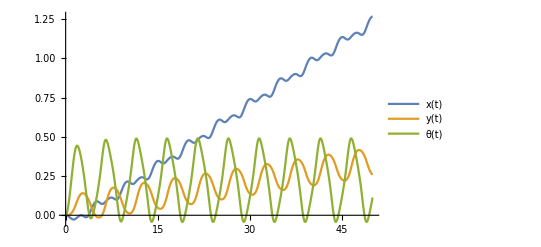

```mathematica
Plot[Evaluate[{x[t], y[t], θ[t]} /. solutionControl], {t, 0, duration},PlotLegends->{x[t],y[t],θ[t]}]
```

```mathematica
movieFrame[time_]:=Show[{body,head,tail,tailPivotLine1,tailPivotDot,tailPivotLine2,headPivotDot,headPivotLine1,headPivotLine2}/.robotParameters/.shapeChange/.solutionControl/.t-> time,PlotRange-> {{-(6 b + gap + 2) , 6 b + gap + 2}, {-(6 b + gap + 2) , 6 b + gap + 2}} /. robotParameters];
```

```mathematica
numberOfFrames = 300;
```

```mathematica
movieFrames = Table[movieFrame[k],{k,0,duration,duration/numberOfFrames}];
```

```mathematica
ListAnimate[movieFrames];
```

```mathematica
FL = {D[L,x'[t]],D[L,y'[t]],D[L,θ'[t]],D[L,ϕ'[t]],D[L,θ1'[t]]};
```

We define the momentum map by <J(v_q),η> which equals <FL(v_q),η_Q(q)>

```mathematica
J1 = (FL.ζQ)/ζ1/.{ζ2-> 0,ζ3-> 0};
```

```mathematica
J2 = (FL.ζQ)/ζ2/.{ζ1-> 0,ζ3-> 0};
```

```mathematica
J3 = (FL.ζQ)/ζ3/.{ζ2-> 0,ζ1-> 0};
```

```mathematica
testCase1={θ[t]-> 0, ϕ[t]-> 0, θ1[t]-> 0,θ'[t]-> 0, ϕ'[t]-> 0, θ1'[t]-> 0};
```

```mathematica
J1/.testCase1
```

3 mLong x'[t]

```mathematica
J2/.testCase1
```

3 mLat y'[t]

```mathematica
J3/.testCase1//FullSimplify
```

-3 mLong y[t] x'[t]+3 mLat x[t] y'[t]

```mathematica
testCase2 = {θ[t]-> 0, ϕ[t]-> 0, x'[t]-> 0, y'[t]-> 0, ϕ'[t]-> 0, θ1'[t]-> 0,θ1[t]-> 0};
```

```mathematica
J1/.testCase2
```

0

```mathematica
J2/.testCase2
```

0

```mathematica
J3/.testCase2//Simplify
```

(8 b^2 mLat+16 b gap mLat+8 gap^2 mLat+3 mRot) θ'[t]

```mathematica
testCase2Verification = (mRot+2 (mRot + mLat (2 b + 2 gap )^2)) θ'[t];
```

```mathematica
Simplify[(J3/.testCase2)-testCase2Verification]
```

0

Everything so far is commensurate with Scott’s analysis of a similar 3-link swimmer. Let’s get to the good stuff. We will, as per Scott’s analysis, need the locked inertia tensor, the connection form, and the local connection form.

```mathematica
rightpairing = λQ.FL/.{x'[t]-> ζQ[[1]],y'[t]-> ζQ[[2]],θ'[t]-> ζQ[[3]],ϕ'[t]-> ζQ[[4]],θ1'[t]-> ζQ[[5]]};
```

```mathematica
lockedInertiaTensor = {{(rightpairing/.{ζ2-> 0,ζ3-> 0,λ2-> 0,λ3-> 0})/(ζ1 λ1),(rightpairing/.{ζ1-> 0,ζ3-> 0,λ2-> 0,λ3-> 0})/(ζ2 λ1),(rightpairing/.{ζ1-> 0,ζ2-> 0,λ2-> 0,λ3-> 0})/(ζ3 λ1)},{(rightpairing/.{ζ2-> 0,ζ3-> 0,λ1-> 0,λ3-> 0})/(ζ1 λ2),(rightpairing/.{ζ1-> 0,ζ3-> 0,λ1-> 0,λ3-> 0})/(ζ2 λ2),(rightpairing/.{ζ1-> 0,ζ2-> 0,λ1-> 0,λ3-> 0})/(ζ3 λ2)},{(rightpairing/.{ζ2-> 0,ζ3-> 0,λ2-> 0,λ1-> 0})/(ζ1 λ3),(rightpairing/.{ζ1-> 0,ζ3-> 0,λ2-> 0,λ1-> 0})/(ζ2 λ3),(rightpairing/.{ζ1-> 0,ζ2-> 0,λ1-> 0,λ2-> 0})/(ζ3 λ3)}};
```

```mathematica
Γ=Inverse[lit].{J1,J2,J3};
```

```mathematica
Adg = {{Cos[θ[t]],-Sin[θ[t]],y[t]},{Sin[θ[t]],Cos[θ[t]],-x[t]},{0,0,1}};
```

```mathematica
localLIT = Transpose[Adg].lockedInertiaTensor.Adg;
```

The following verification checks out when the joint angles are zero. Huzzah!

```mathematica
localLIT/.{ϕ[t]-> 0,θ1[t]-> 0}//Simplify//MatrixForm
```

(3 mLong | 0 | 0
0 | 3 mLat | 0
0 | 0 | 8 b^2 mLat+16 b gap mLat+8 gap^2 mLat+3 mRot)

```mathematica
SE2BV = {x'[t] Cos[θ[t]] + y'[t] Sin[θ[t]], y'[t] Cos[θ[t]] -x'[t] Sin[θ[t]], θ'[t]};
```

A mechanical connection is given by Γ=A(r) rdot + g^-1 gdot=A(r) rdot + SE2BV

```mathematica
g = {{Cos[θ[t]],-Sin[θ[t]], x[t]},{Sin[θ[t]],Cos[θ[t]], y[t]},{0,0,1}};
```

```mathematica
Inverse[g].D[g,t]//FullSimplify//MatrixForm
```

(0 | -θ'[t] | Cos[θ[t]] x'[t]+Sin[θ[t]] y'[t]
θ'[t] | 0 | -Sin[θ[t]] x'[t]+Cos[θ[t]] y'[t]
0 | 0 | 0)

Okay, great. Just wanted to check my understanding of how we represent the body velocity. I now recall that we represent the above matrix as a 3x1 vector.

```mathematica
A = Inverse[Adg].Γ - SE2BV;
```

Much like Scott’s approach to finding the local connection form, I will not wait for Mathematica to simplify A. How can I exploit what I know A should look like so as to require less from Mathematica computationally?

## Q-learning for Varying Stiffness and Amplitude

We want to determine the optimal way to vary the stiffness of a spring in the three-link swimmer over some specified number of cycles. This seems like a good starting point. We can then add the amplitude variation after successfully optimizing the spring stiffness.

```mathematica
PEtailk = 1/2 k1 θ1[t]^2;
```

```mathematica
Lk = KEbody+KEhead+KEtail-PEtailk;
```

```mathematica
xodek = D[D[Lk,x'[t]],t]-D[Lk,x[t]]==0;
```

```mathematica
yodek = D[D[Lk,y'[t]],t]-D[Lk,y[t]]==0;
```

```mathematica
θodek = D[D[Lk,θ'[t]],t]-D[Lk,θ[t]]==0;
```

```mathematica
θ1odek = D[D[Lk,θ1'[t]],t]-D[Lk,θ1[t]]==-c1 θ1'[t];
```

```mathematica
ϕodek = D[D[Lk,ϕ'[t]],t]-D[Lk,ϕ[t]]==0;
```

```mathematica
odesk ={xodek,yodek,θodek,θ1odek,ϕodek};
```

Some functions we will need to define are QUpdate[saPair_, reward_, currentQ_], Reward[state], and sol(defined above). I should first define the learning problem. What is the environment, agent, etc.?

PSEUDOCODE

Establish Q matrix, states, and actions.
Define terminal state

Start a loop:
	Initialize state
	Start another loop:
		Choose the action based on the policy
		Take action, observe reward and next state
		Update Q function
		Update state
	until S is terminal

```mathematica
rlmodel=-Graphics-;
```

```mathematica
rlmodel
```

-Graphics-

Define the reward to be how far the robot moved in the x direction for that cycle. States are x (or omit x), θ, ϕ, θ1, and d/dt θ1. Actions are choices of amplitude and spring stiffness throughout a cycle. Define an episode to be n cycles of a sinusoidal signal. Vary amplitude and stiffness throughout that episode.

Define learning rate, discount factor, time step

```mathematica
θstates = Range[0.0,2π,π/2];
θ1states=Range[0.0,2π,π/2];
ϕstates=Range[-π/2,π/2,π/2];
θ1dotstates=Range[-π/2,π/2,π/2];
ϕdotAction=Range[0.0,0.2,1/20];
stiffnessAction=Range[0.5,2.0,1/2];
```

```mathematica
(*Solve[odesk, {ϕ''[t],θ''[t],x''[t],y''[t],θ1''[t]}]*)
```

```mathematica
α=0.9;
```

```mathematica
γ=0.99;
```

```mathematica
δt=1;
```

```mathematica
eps=0.2;
```

```mathematica
Reward[currentSol_,pastSol_]:=currentSol-pastSol;
```

```mathematica
QUpdate[newPos_,oldPos_,actionPos_,reward_,Q_]:=Q[[newPos[[1]],newPos[[2]],newPos[[3]],newPos[[4]],actionPos[[1]],actionPos[[2]]]]+α (reward+γ Max[ Q[[newPos[[1]],newPos[[2]],newPos[[3]],newPos[[4]]]]]-Q[[oldPos[[1]],oldPos[[2]],oldPos[[3]],oldPos[[4]],actionPos[[1]],actionPos[[2]]]]);
```

```mathematica
Q=Table[0.0,{s1,1,Length[θstates]},{s2,1,Length[θ1states]},{s3,1,Length[θ1dotstates]},{s4,1,Length[ϕstates]},{a1,1,Length[ϕdotAction]},{a2,1,Length[stiffnessAction]}];
```

```mathematica
getActionPos[action_]:={Position[stiffnessAction,action[[1]]][[1]][[1]],Position[ϕdotAction,action[[2]]][[1]][[1]]};
```

When indexing this Q matrix, do so as follows. Q[[s1,s2,s3,s4,a1,a2]].

We could define an epsilon that decays as the number of episodes increases.

```mathematica
ϕdotChange[a_] := {ϕ'[t]->a};
```

```mathematica
getMaxPos[state_,Q_]:=Position[Q[[state[[1]],state[[2]],state[[3]],state[[4]]]],Max[Q[[state[[1]],state[[2]],state[[3]],state[[4]]]]]][[1]];
```

```mathematica
chooseAction[eps_,state_,Q_]:= If[eps>Random[],action={RandomChoice[stiffnessAction],RandomChoice[ϕdotAction]},action={stiffnessAction[[getMaxPos[state,Q][[1]]]],ϕdotAction[[getMaxPos[state,Q][[2]]]]}];
```

```mathematica
takeAction[action_,initialCon_,time_]:=NDSolve[{odesk/.{c1-> 1}/.ellipseMasses/.{k1-> action[[1]]}/.ϕdotChange[action[[2]]]/.{ρ-> 1000}/.robotParameters,initialCon},{x[t],y[t],θ[t],x'[t],y'[t],θ'[t],θ1[t],θ1'[t],ϕ[t],ϕ'[t]},{t,time, time+δt},Method->{"EquationSimplification"-> "Residual"}];
```

Let’s troubleshoot the iterative solution scheme used in the algorithm...
This happens seemingly randomly so I’m going to loop through the following several lines to see if it works...

```mathematica
(*initialConditions={x[0]==0,y[0]==0,θ[0]==0,x'[0]==0,y'[0]==0,θ'[0]==0,θ1[0]==0,θ1'[0]==0,ϕ[0]==0};*)
```

```mathematica
(*For[n=0,n≤ 5, n++,Print[n];testsol= NDSolve[{odesk/.{c1-> 1}/.ellipseMasses/.{k1-> RandomChoice[stiffnessAction]}/.ϕdotChange[RandomChoice[ϕdotAction]]/.{ρ-> 1000}/.robotParameters,initialConditions},{x[t],y[t],θ[t],x'[t],y'[t],θ'[t],θ1[t],θ1'[t],ϕ[t],ϕ'[t]},{t,n, n+1},Method->{"EquationSimplification"-> "Residual"}];initialConditions=(({x[n]==x[t],y[n]==y[t],θ[n]== θ[t],x'[n]==x'[t],y'[n]==y'[t],θ'[n]==θ'[t],θ1[n]==θ1[t],θ1'[n]==θ1'[t],ϕ[n]==ϕ[t]}/.testsol)/.{t-> (n+1)})[[1]];Print["Done"]]*)
```

```mathematica
(*initialConditions={x[0]==0,y[0]==0,θ[0]==0,x'[0]==0,y'[0]==0,θ'[0]==0,θ1[0]==0,θ1'[0]==0,ϕ[0]==0};*)
```

```mathematica
(*extrak1=RandomChoice[ϕdotAction]*)
```

```mathematica
(*testsol= NDSolve[{odesk/.{c1-> 1}/.ellipseMasses/.{k1-> 0.1}/.ϕdotChange[extrak1]/.{ρ-> 1000}/.robotParameters,initialConditions},{x[t],y[t],θ[t],x'[t],y'[t],θ'[t],θ1[t],θ1'[t],ϕ[t],ϕ'[t]},{t,0,1},Method->{"EquationSimplification"-> "Residual"}];*)
```

```mathematica
(*newPosTest=(({x[1]==x[t],y[1]==y[t],θ[1]== θ[t],x'[1]==x'[t],y'[1]==y'[t],θ'[1]==θ'[t],θ1[1]==θ1[t],θ1'[1]==θ1'[t],ϕ[1]==ϕ[t]}/.testsol)/.{t->1})[[1]]*)
```

```mathematica
(*testsol1=NDSolve[{odesk/.{c1-> 1}/.ellipseMasses/.{k1-> 0.1}/.ϕdotChange[0.2]/.{ρ-> 1000}/.robotParameters,newPosTest},{x[t],y[t],θ[t],x'[t],y'[t],θ'[t],θ1[t],θ1'[t],ϕ[t],ϕ'[t]},{t,1, 2},Method->{"EquationSimplification"-> "Residual"}];*)
```

```mathematica
(*newPosTest1=(({x[2]==x[t],y[2]==y[t],θ[2]== θ[t],x'[2]==x'[t],y'[2]==y'[t],θ'[2]==θ'[t],θ1[2]==θ1[t],θ1'[2]==θ1'[t],ϕ[2]==ϕ[t]}/.testsol1)/.{t->2})[[1]];*)
```

```mathematica
(*testsol2=NDSolve[{odesk/.{c1-> 1}/.ellipseMasses/.{k1-> 0.1}/.ϕdotChange[0.2]/.{ρ-> 1000}/.robotParameters,newPosTest1},{x[t],y[t],θ[t],x'[t],y'[t],θ'[t],θ1[t],θ1'[t],ϕ[t],ϕ'[t]},{t,2, 3},Method->{"EquationSimplification"-> "Residual"}];*)
```

```mathematica
(*((x[t]/.testsol2)/.{t-> (3)})[[1]]*)
```

```mathematica
numOfEpisodes = 60;
```

```mathematica
lengthOfEpisode=20;
```

```mathematica
getStatePos[state_]:={Position[states,state[[1]]][[1]],Position[states,state[[2]]][[1]],Position[states,state[[3]]][[1]],Position[states,state[[4]]][[1]]};
```

```mathematica
getClosestStatePos[delta_]:={θStateDelta=delta[[1]];
θ1StateDelta=delta[[2]];
θ1dotStateDelta=delta[[3]];
ϕStateDelta=delta[[4]]; closest = {Position[θStateDelta,Min[θStateDelta]][[1]][[1]],Position[θ1StateDelta,Min[θ1StateDelta]][[1]][[1]],Position[θ1dotStateDelta,Min[θ1dotStateDelta]][[1]][[1]],Position[ϕStateDelta,Min[ϕStateDelta]][[1]][[1]]}};
```

```mathematica
getInitialPos[state1_,state2_,state3_,state4_]:={Position[state1,0.][[1]][[1]],Position[state2,0.][[1]][[1]],Position[state3,0][[1]][[1]],Position[state4,0][[1]][[1]]};
```

```mathematica
(*Initialize Q matrix, states, actions, and terminal state (defined as the maximum time one can wander through the state space)*)
θstates = Range[0.0,2π,π/2];
θ1states=Range[0.0,2π,π/2];
ϕstates=Range[-π/2,π/2,π/2];
θ1dotstates=Range[-π/2,π/2,π/2];
ϕdotAction=Range[0.0,0.2,1/20];
stiffnessAction=Range[0.5,2.0,1/2];
states={θstates,θ1states,θ1dotstates,ϕstates};
Q=Table[0.0,{s1,1,Length[θstates]},{s2,1,Length[θ1states]},{s3,1,Length[θ1dotstates]},{s4,1,Length[ϕstates]},{a1,1,Length[stiffnessAction]},{a2,1,Length[ϕdotAction]}];
(*Run a series of episodes*)
For[i=1, i≤ numOfEpisodes, i++,initialConditions={x[0]==0,y[0]==0,θ[0]==0,x'[0]==0,y'[0]==0,θ'[0]==0,θ1[0]==0,θ1'[0]==0,ϕ[0]==0};
(*Initialize *)
statePos=getInitialPos[θstates,θ1states,θ1dotstates,ϕstates]; pastx=0;
(*Take "lengthOfEpisode" steps in the environment*)
For[j=0, j< lengthOfEpisode, j++,
(*Choose the action from current state using desired policy*)
action=chooseAction[eps,statePos,Q];actionPos=getActionPos[action];
 (*Take action and observe distance in x direction (reward)*)
solution=takeAction[action,initialConditions,j];
newx=((x[t]/.solution)/.{t-> (j+δt)})[[1]];
(*Observe new state*)
newState=(({θ[t],θ1[t],θ1'[t],ϕ[t]}/.solution)/.{t-> j})[[1]];
(*Determine which discretized state newState is closest to. Really this finds the closest position in the set of states and returns it so it can be matched in the Q matrix.*)
delta=states-newState;
newStatePos=getClosestStatePos[delta][[1]];
(*Compute reward*)
r=Reward[newx,pastx];
pastx=newx;
(*Update Q matrix. Be sure to add Q[currentstate]=QUpdate*)
Q[[newStatePos[[1]],newStatePos[[2]],newStatePos[[3]],newStatePos[[4]],actionPos[[1]],actionPos[[2]]]]=QUpdate[newStatePos,statePos,actionPos,r,Q];
statePos=newStatePos;initialConditions=(({x[j]==x[t],y[j]==y[t],θ[j]== θ[t],x'[j]==x'[t],y'[j]==y'[t],θ'[j]==θ'[t],θ1[j]==θ1[t],θ1'[j]==θ1'[t],ϕ[j]==ϕ[t]}/.solution)/.{t->j})[[1]]];Print["Done"]]
```

Done

Done

Done

«57 more identical outputs»

```mathematica
Q[[1,1,1,1]]
```

{{1.48566×10^10,1.42037×10^10,9.82903×10^8,2.94937×10^9,2.80366×10^9},{8.59774×10^9,8.41467×10^9,5.35639×10^9,5.33591×10^9,8.86989×10^9},{8.81076×10^9,5.02716×10^9,8.65962×10^7,3.52062×10^8,1.65226×10^9},{1.49261×10^10,497.681,7.25234×10^6,8.9217×10^9,1.90877×10^7}}

```mathematica
Dimensions[Q]
```

{5,5,3,3,4,5}

The algorithm seems to run without throwing any errors. Let’s now think about how we will extract the policy and simulate the system using that policy...